## I.Ellipse

### The graph of the equation (x/a)^2+(y/b)^2=1, with -a≤ x ≤a, -b≤ y≤ b is an ellipse.

#### iii. Find the volume of the solid of by rotating this ellipse about the x-axis. Hint: First find the volume of the solid of revolution of the first-quadrant portion, y=b(1-(x/a)^2)^(1/2), 0≤ x ≤a, about the x-axis and multiply it by 2. Then, with a=3 and b=5, plot the solid of revolution about the x-axis using the built-in syntax of Mathematica.

We have a function y=b(1-(x/a)^2)^(1/2),  0≤ x ≤a

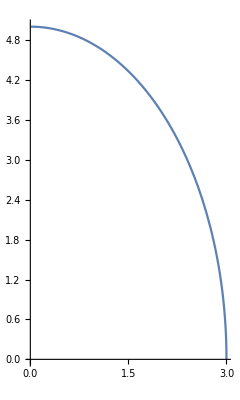

```mathematica
Plot[5(1-(x/3)^2)^(1/2),{x,0,3},AspectRatio->Automatic]
```

Solve the first quadrant of the ellipse and multiply it by 2

```mathematica
Solve[∫_0^a π*(b(1-(x/a)^2)^(1/2))^2 ⅆx]
```

Solve[2/3 a b^2 π]

```mathematica
Manipulate[RevolutionPlot3D[(5 √(3^2-x^2))/3,{x,0,10},{t,0,tt},RevolutionAxis->{1,0,0}],{tt,.1,2π}]
```

Multiply it by 2 and plotting a and b

```mathematica
Solve[(2/3 3 5^2 π)*2]
```

Solve[100 π]

```mathematica
RevolutionPlot3D[(5 √(3^2-x^2))/3,{x,-10,10},RevolutionAxis->{1,0,0}]
```

-Graphics3D-

## II.Torus

### The disks x^2+y^2 ≤a is revolved about the line x=b (b>a) to generate a solid shaped like a doughnut called a torus. Plot the torus with a=2 and b=5.

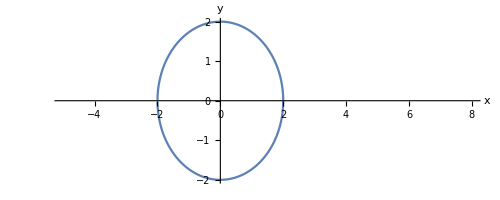

```mathematica
Plot[y/. Solve[x^2+y^2==2^2],{x,-5,8},
AxesLabel->{"x","y"},
PlotLegends->"Expressions",
AspectRatio->Automatic
]
```

V=∫_-r^r π(A(y)^2-a(y)^2)ⅆy
(x-R)^2+y^2=r^2
x=R+-√(r^2-y^2)
A(y)=R+√(r^2-y^2)
a(y)=R-√(r^2-y^2)
=>π∫_-r^r ((R+√(r^2-y^2))^2-((R-√(r^2-y^2))^2)ⅆy
=π∫_-r^r (4R √(r^2-y^2))ⅆy
V=4πR∫_-r^r (√(r^2-y^2))ⅆy
=4πR(1/2πr^2)
V=2π^2r^2R

```mathematica
Solve[2 π^2*2^2*5]
```

Solve[40 π^2]

```mathematica
Graphics3D[Torus[{5,0,0},{3,7}],Axes->True]
```

-Graphics3D-

```mathematica
Manipulate[RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2Pi},{d,0,dd}],{dd,.1,2π}]
```

## III. Asteroid

### The graph of the equation x^(2/3)+y^(2/3)=1, with -1≤x≤1, -1≤y≤1 is called an “Asteroid” because of its starlike appearance.

#### iii. Find the volume of the solid by rotating this asteroid about the x-axis . Hint: First find the volume of the solid of revolution of the first quadrant portion. y=(1-x^(2/3))^(3/2), 0≤x≤1, about the x-axis and multiply it by . Then, plot the solid of revolution about the x-axis using the built-in syntax of Mathematica.

We have a function y=(1-x^(2/3))^(3/2), 0≤x≤1

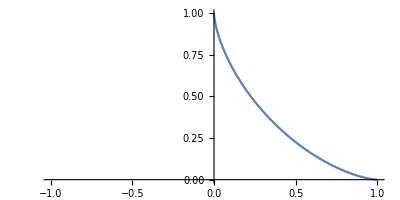

```mathematica
Plot[(1-x^(2/3))^(3/2),{x,-1,1},AspectRatio->Automatic]
```

Solve the first quadrant of the asteroid

```mathematica
Solve[∫_0^1 π*((1-x^(2/3))^(3/2))^2 ⅆx]
```

Solve[(16 π)/105]

```mathematica
Manipulate[RevolutionPlot3D[(1-x^(2/3))^(3/2),{x,0,1},{t,0,tt},RevolutionAxis->{1,0,0}],{tt,.1,2π}]
```

Multiply it by 2

```mathematica
Solve[(16 π)/105*2]
```

Solve[(32 π)/105]

```mathematica
Rev2=RevolutionPlot3D[√(1-3 (-x)^(2/3)+3 (-x)^(4/3)-(-x)^2),{x,-1,1},RevolutionAxis->{1,0,0}];
```

```mathematica
Rev1=RevolutionPlot3D[(1-x^(2/3))^(3/2),{x,-1,1},RevolutionAxis->{1,0,0}];
```

```mathematica
Show[Rev1,Rev2,PlotRange->All]
```

-Graphics3D-